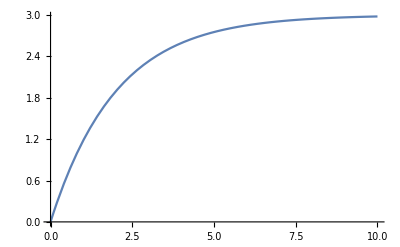

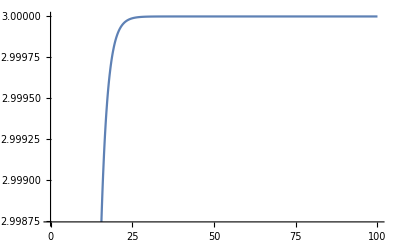

```mathematica
r=1;
v=3;
l=2;
Plot[ v/r(1- Exp[-r*t/l]),{t,0,10}]
Plot[ v/r(1- Exp[-r*t/l]),{t,0,100}]
```

```mathematica
FourierSeries[Abs[Sin[t]],t,10]
```

2/π-(2 ⅇ^(-2 ⅈ t))/(3 π)-(2 ⅇ^(2 ⅈ t))/(3 π)-(2 ⅇ^(-4 ⅈ t))/(15 π)-(2 ⅇ^(4 ⅈ t))/(15 π)-(2 ⅇ^(-6 ⅈ t))/(35 π)-(2 ⅇ^(6 ⅈ t))/(35 π)-(2 ⅇ^(-8 ⅈ t))/(63 π)-(2 ⅇ^(8 ⅈ t))/(63 π)-(2 ⅇ^(-10 ⅈ t))/(99 π)-(2 ⅇ^(10 ⅈ t))/(99 π)

```mathematica
FullSimplify[%]
```

-(2 (11 (-315+210 Cos[2 t]+42 Cos[4 t]+18 Cos[6 t]+10 Cos[8 t])+70 Cos[10 t]))/(3465 π)

```mathematica
FourierCosCoefficient[Abs[Sin[t]],t,n]
```

-(2 (1+(-1)^n))/((-1+n^2) π)

FourierCosCoefficient[Abs[Sin[C t]],t,n]

```mathematica
FourierCosCoefficient[Abs[Sin[t]],t,0]
```

4/π

```mathematica
FourierCosCoefficient[Abs[Sin[t]],t,1]
```

0

```mathematica
FourierSinCoefficient[Abs[Sin[t]],t,n]
```

0

```mathematica
sin(bT)∫tcos(bt)*e^(-at)dt) (from 0 to T)-(cos(bT))∫tsin(bt)*e^(-at)dt (from 0 to T)
```

```mathematica
FullSimplify[Sech[ x] *ArcTanh[Sinh[ x]/(√(Sinh^2(x)+V+1))]]
```

ArcTanh[Sinh[x]/(√(1+V+Sinh^2 x))] Sech[x]